# Code to accompany the paper: “Using IFS to Reveal Biases in the Distribution of Prime Numbers” by Harlan J. Brothers In Fractals: https://www.worldscientific.com/doi/10.1142/S0218348X24501032

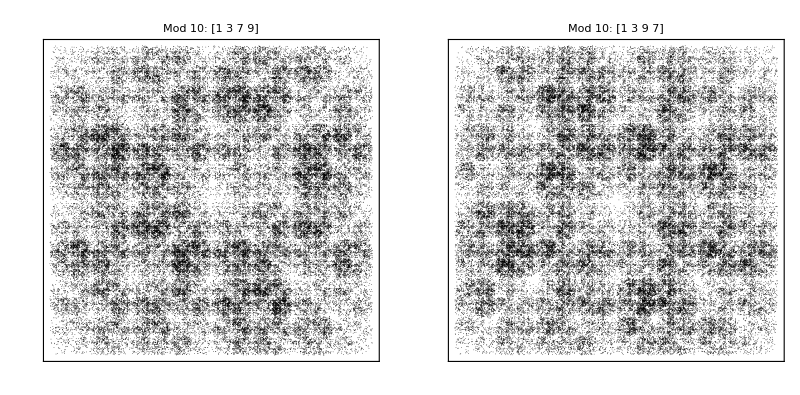

```mathematica
divider=2;(* Set grid divisions for x and y *)
grid=Table[k/divider,{k,1,divider-1}];
coPrime[k_]:=Select[Range[k],CoprimeQ[#,k]==True&];
perm=Permutations[{1,2,3,4}][[;;2]];

ifsPlots:=Module[
{a,b,c,d},If[!MemberQ[{5,8,10,12},mod],{Print[Style["Please choose modulus 5, 8, 10, or 12",14]],Abort[]}] ;
Do[
cp[i]=coPrime[mod][[perm[[i]]]];
Thread[{a,b,c,d}=perm[[i]]];
tranformOrder[i]=Switch[Mod[#,mod],coPrime[mod][[1]],a,coPrime[mod][[2]],b,coPrime[mod][[3]],c,coPrime[mod][[4]],d]&/@Prime[Range[start,start+span-1]];
f[j_,{x_,y_}]:=0.5*{x,y}+0.5*Reverse[IntegerDigits[j-1,2,2]];
pt={0.5,0.5};
ptlst=Table[pt=f[tranformOrder[i][[j]],pt],{j,Length[tranformOrder[i]]}];
plts[i]=ListPlot[ptlst,
Frame->True,
FrameStyle->Directive[RGBColor[0,.5,.8],Thickness[.006]],
FrameTicks->None,
Axes->True,
GridLines->{grid,grid},GridLinesStyle->Directive[RGBColor[0,.5,.8],Thickness[.002]],
PlotRange->{{0,1},{0,1}},
PlotStyle->{PointSize->ptSize,Black},AspectRatio->1,PlotLabel->Style["Mod "<>ToString@mod<>": ["<>ToString@cp[i][[1]]<>" "<>ToString@cp[i][[2]]<>" "<>ToString@cp[i][[3]]<>" "<>ToString@cp[i][[4]]<>"]",13],
ImageSize->imgSize],
{i,2}];
display[mod]=GraphicsRow[{plts[1],plts[2]},Spacings->12]
]

(* Choose parameters *)
start=4;span=100000;imgSize=480;ptSize=.001;mod=10;
ifsPlots
```